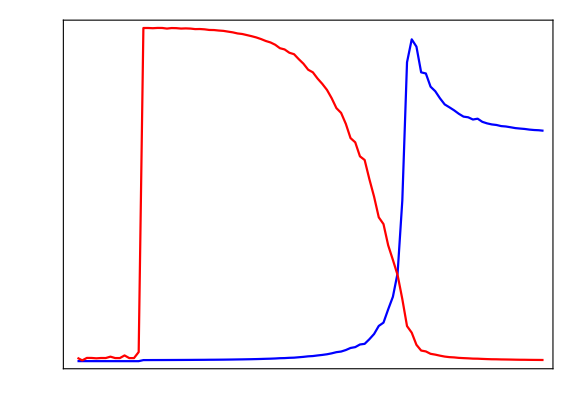

```mathematica
dataIPR = Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/IPR.dat"];
dataFidel = Import["/Users/apatron/Desktop/codes/metropolis/numerical diagonalisation/Fid.dat"];
LineCDW = Line[{{1.37,-0.1},{1.37,1.2}}];
LineRej = Line[{{2.72,-0.1},{2.72,1.2}}];
Show[ListLinePlot[dataIPR,PlotStyle->Blue],ListLinePlot[dataFidel,PlotStyle->Red],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->{{MaTeX["",Magnification->2],None},MaTeX[{"a","\\alpha = 1.22, \\ \\text{IPR (blue) and Fidelity (red)}"},Magnification->2]},ImageSize->Large,AspectRatio->0.7,PlotRange->{{1,3.5},{0,1}},FrameTicks->{{Table[{0.2*i,MaTeX[NumberForm[0.2*i,{2,1}],Magnification->2]},{i,0,7}],None},{Table[{1+0.5*i,MaTeX[NumberForm[1+0.5*i,{2,1}],Magnification->2]},{i,0,7}],None}},Epilog->{Directive[Black,Dashed],{LineCDW,LineRej}}]
```